```mathematica
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
c=300000
h=0.71;
H0=100 h;
d1=6 Ωx0/Ωm0;
```

300000

```mathematica
H[a_]=H0 √(Ωx0 +Ωm0 a^-3+Ωr0 a^-4)
f[a_]=12(H[a]/c)^2+6a H[a]/c D[H[a]/c,a]
f1[a_]=D[12(H[a]/c)^2+6a H[a]/c D[H[a]/c,a],a]//Simplify
```

71. √(0.73+0.0000809/a^4+0.27/a^3)

6.72133×10^-7 (0.73+0.0000809/a^4+0.27/a^3)+1.68033×10^-7 (-0.0003236/a^5-0.81/a^4) a

-(1.36107×10^-7)/a^4

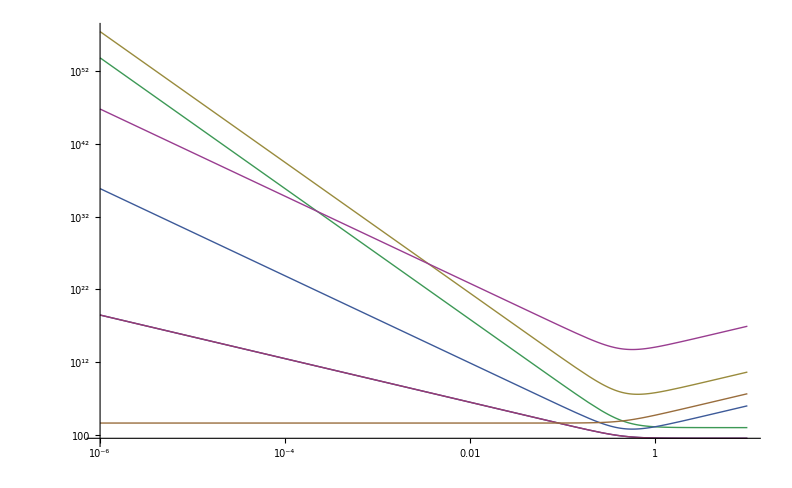

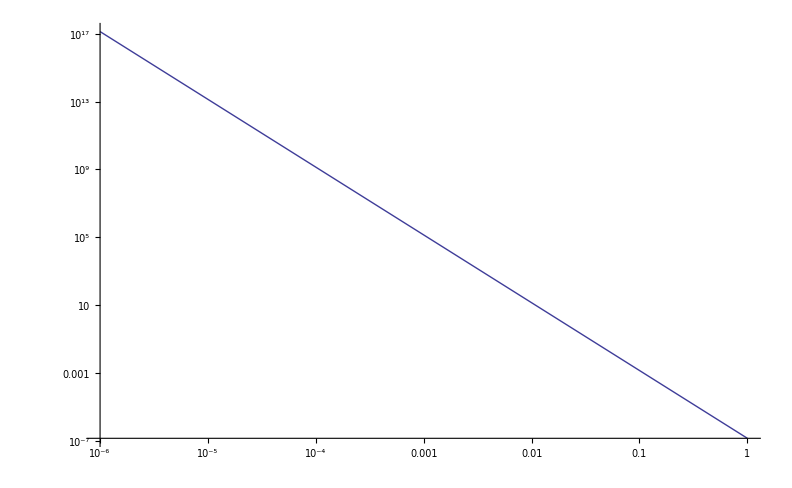

4.03326

8.01712

28.7296

-16.8941-6.90417 x

```mathematica
LogLogPlot[{f[a]/(H0^2 Ωm0)c^2,(3 H0^2/c^2(Ωm0 a^-3+4 Ωx0))/(H0^2 Ωm0)c^2,f[a]^4/a^-3 c^6,f[a]^3 c^4,f[a]^3/a^-3 c^4,f[a]^3/a^-3 c^6,f[a]/a^-3 c^2},{a,0.000001,10},PlotRange->Full]
LogLogPlot[-f1[a],{a,0.000001,1}]
Log[f[0.5]/(H0^2 Ωm0)c^2]
Log[f[0.1]/(H0^2 Ωm0)c^2]
Log[f[10^-4]/(H0^2 Ωm0)c^2]
Fit[{{-1,Log[f[0.1]]},{-4,Log[f[10^-4]]}},{1,x},x]
```

R/m^2>>1 so that f(R) can be expanded!!!!!

```mathematica
Series[c1/(c2+tmp),{tmp,0,3}]
```

c1/c2-(c1 tmp)/c2^2+(c1 tmp^2)/c2^3-(c1 tmp^3)/c2^4+O[tmp]^4

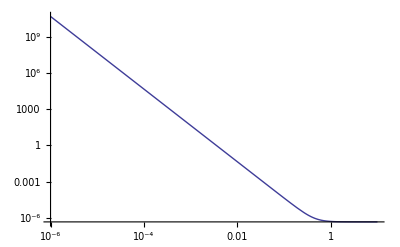

LogLogPlot::argr: LogLogPlot called with 1 argument; 2 arguments are expected.

LogLogPlot[32.4444+(3 HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/mass^2]

```mathematica
LogLogPlot[3 H0^2/c^2 Ωm0(a^-3+4 Ωx0/Ωm0),{a,0.000001,10},PlotRange->Full]
LogLogPlot[32.44444444444444+(3 HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/mass^2]
```